```mathematica
f[μ_,x_]:= μ x (1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
(*Manipulate[ListPlot[fn[μ,0.4,#]&/@Range[100]],{μ,0,4}]*)
```

```mathematica
conf[μ_,n_,precision_]:=Length[Union[Round[10^4(fn[μ,0.4,300+#]-fn[μ,0.4,300]),precision]& /@Range[2^n]]]
```

```mathematica
data= ParallelTable[{μ,conf[μ,7]},{μ,2.8,3.5,10^-5}];
```

```mathematica
(*fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ #(1-#)&,x,n]]*)
```

CompiledFunction[…]

Ci metterebbe 12 anni a computarlo mi sa, io per sicurezza faccio npo a mano

#### Troviamo i punti a manina:

```mathematica
data0= ParallelTable[{μ,conf[μ,2,1]},{μ,2.8,3.1,10^-4}];
```

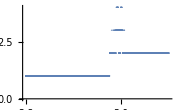

```mathematica
ListPlot[data0]
```

```mathematica
First@Last@Cases[data0,{_,1}]
```

2.9759

```mathematica
data1=ParallelTable[{μ,conf[μ,4,10]},{μ,3.1,3.5,10^-4}];
```

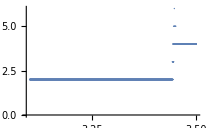

```mathematica
ListPlot[data1]
```

```mathematica
First@Last@Cases[data1,{_,2}]
```

3.4438

```mathematica
data2=ParallelTable[{μ,conf[μ,5,10]},{μ,3.5,3.57,10^-5}];
```

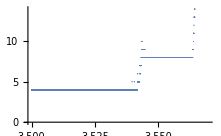

```mathematica
ListPlot[data2]
```

```mathematica
First@Last@Cases[data2,{_,4}]
```

3.54182

```mathematica
First@Last@Cases[data2,{_,8}]
```

3.56375

```mathematica
data3=ParallelTable[{μ,conf[μ,6,1]},{μ,3.564,3.57,10^-5}];
```

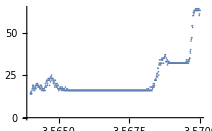

```mathematica
ListPlot[data3]
```

```mathematica
First@Last@Cases[data3,{_,16}]
```

3.5683

```mathematica
First@Last@Cases[data3,{_,32}]
```

3.56959

```mathematica
data4=ParallelTable[{μ,conf[μ,7,1]},{μ,3.565,3.5702,10^-6}];
```

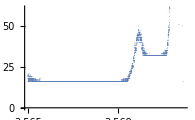

```mathematica
ListPlot[data4]
```

```mathematica
First@Last@Cases[data4,{_,64}]
```

3.56988

μ_∞≈3.57

```mathematica
data=Flatten[{data0,data1,data2,data3,data4},1];
```

#### da concludere

fare un data =Flatten[ {data_1,...,data_n}] o farlo computare un po’ con quella iniziale (o pi

```mathematica
μ[n_]:= First@Last@Cases[data,{_,2^n}]
```

```mathematica
feigenbaum =Table[(μ[n]-μ[n-1])/(μ[n+1]-μ[n]),{n,1,5}]
```

{4.77352,4.46968,4.7924,3.53906,4.99228}

eh. e mo?
tranne il quarto valore possiamo vedere che i numeri sono vicini

possiamo fare una media geometrica brutalmente

```mathematica
GeometricMean[Drop[feigenbaum,{4}]]
```

4.75326

ha senso farlo?
probabilmente nO! (ma sticazzi)
la costante è circa quella, con dati più precisi si potrebbe far meglio ma dovrei lavorarci sopra e sono pigro.